### Constants and Initial Conditions

```mathematica
(*Non-dimensional Momentum Range*)
n=100.;
ymax=20.;
ymin=0.01;
hy=(ymax-ymin)/(n-1.);
y1=Table[i,{i,ymin,ymax,hy}];
(*Initial Non-dimensional Temperature and Time*)
zin=1.00003;
m=50.;
xin=me/10.;xfin=30.;
hx=(xfin-xin)/(m-1.);
```

```mathematica
(*All Parameters in MeV*)
me=0.511;
Mpl=1.22091 10^19 10^3;
GF=1.1663787 10^-5 10^-6;
gL=0.727;
gR=0.233;
gμL=-0.273;
```

```mathematica
(*Interpolation Order*)
interpOrder=10;
```

```mathematica
(*Solver Parameters*)
AG=6;
MP=1000;
```

### Continuity Equation

```mathematica
(*Internal Integrals*)
F1[μ_]:=NIntegrate[ω^2 Exp[√(ω^2+μ^2)]/((Exp[√(ω^2+μ^2)]+1.)^2),{ω,ymin,ymax}];
F2[τ_]:=NIntegrate[ω^4 Exp[√(ω^2+τ^2)]/((Exp[√(ω^2+τ^2)]+1.)^2),{ω,ymin,ymax}];
```

```mathematica
CE[dfνe_,dfνμ_,z_Real,x_Real]:=1/((x/z)^2 F1[x/z]+F2[x/z]+((2 N[π]^4)/15.))(x/z F1[x/z]-1/(2. z^3)NIntegrate[y^3(dfνe[y]+2.dfνμ[y]),{y,ymin,ymax},AccuracyGoal->10]);
```

```mathematica
Z=NDSolveValue[{z'[x]==CE[0&,0&,z[x],x],z[xin]==zin},z,{x,xin,xfin}]
```

InterpolatingFunction[{{0.0511, 30.}}, <>]

```mathematica
Z[xfin]
```

1.40098

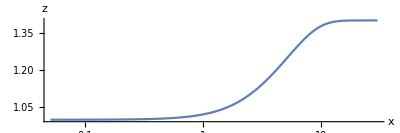

```mathematica
LogLinearPlot[Z[x],{x,xin,xfin},AxesLabel->{"x","z"},AspectRatio->1/3,PlotRange->All]
```